```mathematica
N[Solve[(k1 c2 -1/te-1/ti-k2 c6)/(2 k1 c2)==(-c10-Sqrt[c10 ^2-4 c9 c11])/(2 c9)]]
```

{{Jee→0.0345459-2.01228×10^-16 ⅈ},{Jee→0.62309+7.21645×10^-16 ⅈ}}

```mathematica
(*ce for excitatory gain, ci for inhibitory gain. eIth and iIth the different thresholds *)
ti=2 ; te= 100;   ce = 310 (*gain factor*); ci= 615; Io= 1/10 (*background*); eIth= 125;iIth= 177; Is=1/20(*stimulus*);a=64/100; (*linear estimate for excitaory and inhibitory input-output functions*) k1 = 310/1000;k2=615/1000 ;(*1/1000 for unit consistency*);
```

```mathematica
Io=.3;Jie=.07;Jii=.1; Jee=0.7839946240100992;
```

```mathematica
Clear[Si,Se]
```

```mathematica
Si=k2(c4+c2 Se)/(1/ti + k2 c6);
```

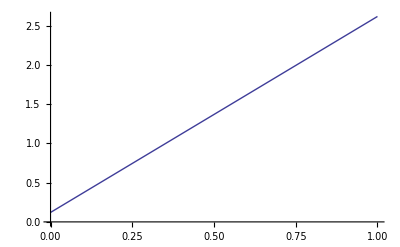

```mathematica
p1=Plot[Si,{Se,0,1}]
```

```mathematica
Clear[Si,Se]
```

```mathematica
Si2=1/c3(c1+c2 Se-Se/(te  k1(1-Se)));
```

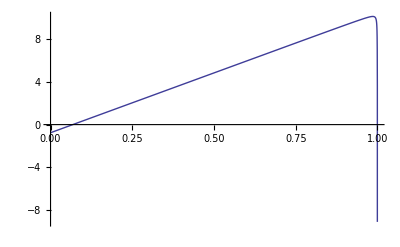

```mathematica
p2=Plot[Si2,{Se,0,1}]
```

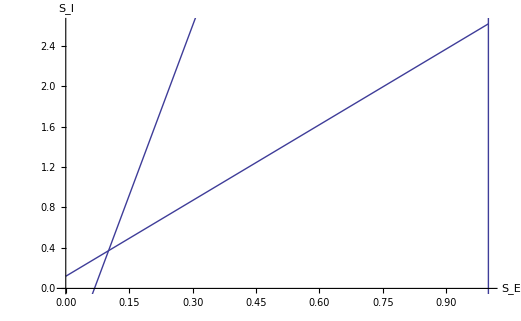

```mathematica
Show[p1,p2,AxesLabel->{"S_E","S_I"}]
```

```mathematica
Solve[Si==Si2]
```

{{Se→0.10122},{Se→0.999703}}

```mathematica
Se=0.1025150382958209;
```

```mathematica
Se=0.10121971750835392;
```

```mathematica
Clear[c7]
```

```mathematica
c7
```

-0.11773

```mathematica
Si
```

0.376256

```mathematica
Si2
```

0.387527

```mathematica
Clear[Se]
```

```mathematica
c7 = 1/te-k1 c2 +2 k1 c2 Se+1/ti +k2 c6
```

-0.124918

```mathematica
c8=1/(te ti)+k2 c6/(te)-k1 c2/ti -k1 c1 k2 c6 + 2 k1 c2 Se/ti+k1 k2 c5 c3+2 k2 c6 k1 c2 Se -k1 k2 c3 c5 Se;
```

```mathematica
Si
```

0.376256

```mathematica
Se=0.10121971750835392
```

0.10122

```mathematica
(*test for saddle point for the other fixed point*)
```

```mathematica
Se=0.9997030802869084;
```